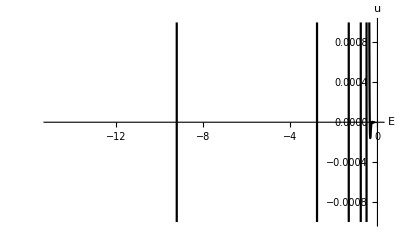

FindRoot::nveq: 方程数与 FindRoot[f[e]==0,{e,-15,-10},MaxIterations→10000,WorkingPrecision→30] 中的变量数不匹配.

{0.270571,FindRoot[f[e]==0,{e,-15,-10},MaxIterations→10000,WorkingPrecision→30]}

```mathematica
u0=10^-6;α=0.262713;
V[r_]:=-14.3996/r+Subscript[V, s][r]
Subscript[V, s][r_]:=1/r^2
f[e_?NumberQ(*/;e∈Reals*)]:=
Block[{u,r,r1=100,r2=10^-6},
First[u[r2]/.
NDSolve[{u''[r]+(α(e-V[r])-0/r^2)u[r]==0,u[r1]==u0,u'[r1]==√(α(V[r1]-e)) u0},
u,{r,r1,r2}(*,MaxStep->10^6,WorkingPrecision->10,MaxStepFraction->10^-3*)]]]//AbsoluteTiming
Plot[{f[e]},{e,-15,0},
PlotRange->{{-15,0}(*,{-8,6}*),{-10^-3,10^-3}},
AxesLabel->{"E","u"},
PlotStyle->Black,PlotPoints->100]
FindRoot[f[e]==0,{e,-15,-10},MaxIterations->10000,WorkingPrecision->30]//AbsoluteTiming
```